# Hands-on Start to Mathematica

## Basic input

```mathematica
627/3
```

209

```mathematica
628/3
```

628/3

```mathematica
N[628/3]
```

209.333

## Free-form input

WolframAlphaQueryParseResults

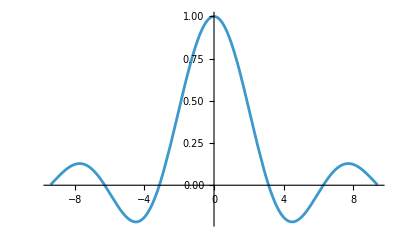

WolframAlphaQueryParseResults

3.141592653589793238462643383279502884197169399375105820974944592307816406286208998628034825342117068

WolframAlphaQueryParseResults

{{x→7/2,y→21/4}}

WolframAlphaQueryParseResults

ArcTan[(-1+2 x)/(√3)]/(√3)+1/3 Log[1+x]-1/6 Log[1-x+x^2]

WolframAlphaQueryParseResults

0

WolframAlphaQueryParseResults

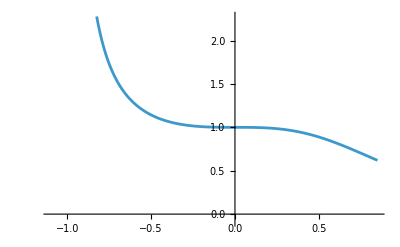

WolframAlphaQueryParseResults

-Graphics3D-

## Wolfram Language input

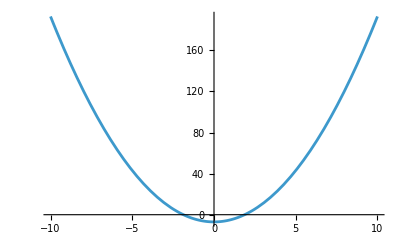

```mathematica
Plot[2x^2-7, {x, -10, 10}]
```

```mathematica
Plot3D[Sin[x y], {x,-3,3}, {y, -3, 3}]
```

-Graphics3D-

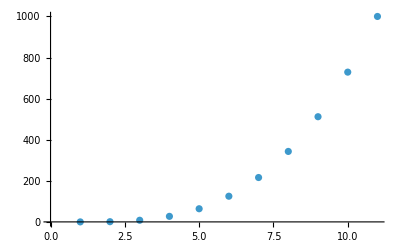

```mathematica
Table[i^3, {i,0,10}];
ListPlot[%]
```

```mathematica
mat1 = {{1,3,-2}, {2,5,0},{-3,-5,7}};
Det[mat1]
```

-17

```mathematica
Clear[mat1]
```

## Applying what we’ve learned

```mathematica
Manipulate[Plot[Sin[freq*x], {x, 0, 6*Pi}, PlotRange -> {-4, 4}],{freq,1,5}]
```

```mathematica
Manipulate[Plot[amp*func[freq*x], {x, 0, 6*Pi}, PlotRange -> {-4, 4}],{freq,1,5}, {amp, 1,4}, {func,{Sin, Cos,Tan}}]
```

## Documentation and saving

## Exercises: Multiparadigm Programming

### Exercise1 Use the Total function to write a functional program that adds up the elements in the list {1,2,3,4,5}

```mathematica
Total[Range[5]]
```

15

### Exercise2 Use Apply to write a functional program that adds up the elements in the list {1,2,3,4,5}

```mathematica
Apply[Plus, Range[5]]
```

15

### Exercise3 Use the rule p_Integer→2p to multiply each integer in the list {2,π,5} by two.

```mathematica
{2,Pi,5} /. p_Integer ->2 p
```

{4,π,10}

### Exercise4 Use Map and a pure function to multiply each integer in the list {2,π,5} by two.

```mathematica
Map[If[IntegerQ[#],2 #,#]&,{2,Pi,5}]
```

{4,π,10}

### Exercise5 Use Count and the pattern _?PrimeQ to do the same calculation as this procedural program: n=0;Do[If[PrimeQ[i],n++],{i,10}];n 4

```mathematica
Count[PrimeQ[Range[10]],PrimeQ[2]]
```

4

```mathematica
Count[Range[10],_?PrimeQ]
```

4

### Exercise6 Use ReplaceAll and a pair of rules to get the same result as from this program: x={1,2,π,4,5}; ​​Do[Which[EvenQ[x[[i]]],x[[i]]/=2,OddQ[x[[i]]],x[[i]]*=10],{i,5}];x {10,1,π,2,50}

```mathematica
{1,2,π,4,5}/. {x_?EvenQ  :> x/2 , x_?OddQ :> x*10}
```

{10,1,π,2,50}

### Exercise7 Use ReplaceRepeated and a rule to get the same result as the result from this program: Nest[If[EvenQ[#],#/2,#]&,80,10] 5

```mathematica
80 //. x_?EvenQ :> x/2
```

5

## Exercises Functional Programming

### Exercise1 Use Map and a pure function to get the same result as the result from this program: x={{2,3},{3,4},{4,5}}; ​​Do[x[[i]]=x[[i,1]]Cos[x[[i,2]]],{i,3}];​​x {2Cos[3],3Cos[4],4Cos[5]}

```mathematica
x={{2,3},{3,4},{4,5}};
Do[x[[i]]=x[[i,1]]Cos[x[[i,2]]],{i,3}];
x
```

{2 Cos[3],3 Cos[4],4 Cos[5]}

```mathematica
x={{2,3},{3,4},{4,5}};
Map[#[[1]]*Cos[#[[2]]] &,x]
```

```mathematica
{{2,3},{3,4},{4,5}}/@ #[[1]]*Cos[#[[2]]] &
```

```mathematica
#⟦1⟧ Cos[#⟦2⟧]& /@{{2,3},{3,4},{4,5}}
```

{2 Cos[3],3 Cos[4],4 Cos[5]}

### Exercise2 Use Apply and a pure function to get the same result as the result from this program: x={{2,3},{3,4},{4,5}}; ​​Do[x[[i]]=x[[i,1]]Cos[x[[i,2]]],{i,3}];​​x {2Cos[3],3Cos[4],4Cos[5]}

```mathematica
x={{2,3},{3,4},{4,5}};
Apply[# Cos[#2]&, x, {1}]
```

```mathematica
{2 Cos[3],3 Cos[4],4 Cos[5]}
Clear[x]
```

{2 Cos[3],3 Cos[4],4 Cos[5]}

### Exercise3 Assign a pure function as the value of a new symbol f so that Map[f,{10,11,12,13,14,15,16}] gives the same result as this program: Map[Function[x,If[#1<3,#1,#2[#1-3,#2]]&[x,If[#1<3,#1,#2[#1-3,#2]]&]],{10,11,12,13,14,15,16}] {1,2,0,1,2,0,1}

```mathematica
Map[Function[x,If[#1<3,#1,#2[#1-3,#2]]&[x,If[#1<3,#1,#2[#1-3,#2]]&]],{10,11,12,13,14,15,16}]
```

{1,2,0,1,2,0,1}

```mathematica
f = If[#<3,#,f[#-3] ] &;
Map[f,{10,11,12,13,14,15,16}]
clear[f];
```

{1,2,0,1,2,0,1}

## Exercises Rule-Based Programming

### Exercise1 Write a rule-based program to do what the Expand function does, using ReplaceRepeated and a rule that replaces any expression of the form p_(q_+r_) with pq+pr.

```mathematica
Expand[5(x+3)]
```

15+5 x

```mathematica
((a+b+1)a+b+1)(x+y+2)//.p_(q_+r_) -> p q+p r
```

2+2 a+2 a^2+2 b+2 a b+x+a x+a^2 x+b x+a b x+y+a y+a^2 y+b y+a b y

### Exercise2 Write a rule-based program to apply sum and multiple angle identities for the cosine function, using ReplaceRepeated, a rule to replace any expression of the form Cos[p_+q_] with Cos[p]Cos[q]-Sin[p]Sin[q], and a rule to replace any expression of the form Cos[n_Integerp_] with Cos[p]Cos[(n-1)p]-Sin[p]Sin[(n-1)p]

```mathematica
Cos[2x-y] //. {Cos[p_+q_] :> Cos[p] Cos[q]-Sin[p] Sin[q],Cos[n_Integer p_]:> Cos[p]Cos[(n-1)p]-Sin[p]Sin[(n-1)p]}
```

Cos[y] (Cos[x]^2-Sin[x]^2)+Sin[2 x] Sin[y]

### Exercise3 Use Nest and ReplaceAll to apply the rules {f[0]→0,f[p_]→f[p-1]} to the expression {f[3],f[11],f[π]} exactly five times

```mathematica
Nest[ReplaceAll[{f[0]->0,f[p_]->f[p-1]}],{f[3],f[11],f[π]},5]
```

{0,2,-3+π}

```mathematica
Nest[(#/.{f[0]->0,f[p_]->f[p-1]})&,{f[3],f[11],f[π]},5]
```

{0,2,-3+π}

## Exercises: Evaluation

```mathematica
Clear[f]
```

### Exercise1 Set an attribute for a symbol f so that f[{1,2},{3,4}] evaluates to {f[1,3],f[2,4]} .

```mathematica
SetAttributes[f,Listable]
f[{1,2},{3,4}]
```

{f[1,3],f[2,4]}

### Define a function S[p_] that holds the argument p unevaluated and that returns the list {Hold[p],p}. For example, the definition of S should give: S[2+2] {Hold[2+2],4}

```mathematica
SetAttributes[S,HoldFirst];S[p_] := {Hold[p], p}
S[2+2]
```

{Hold[2+2],4}

### Exercise3

```mathematica
Hold[Echo[2],Echo[1]]/.Hold[p_,q_]:>With[{x=p,y=q},{y,x}]
```

2

1

{1,2}

```mathematica
Hold[Echo[1],Echo[2]]/.Hold[p_,q_]:>With[{y=q,x=p},{x,y}]
```

2

1

{1,2}

## Exercises: Expressions

### Exercise1 Define a function f[x_,y_] that adds x and y and displays the result in full form notation.

```mathematica
f[x_,y_] := FullForm[x+y]
f[e,r]
```

Plus[e,r]

### Exercise2 Define a pure function a[list_] that counts how many elements of a list are atoms and how many are not.

```mathematica
Ca[list_]:=Counts[AtomQ/@list]
Ca[{1,2.3,"allo", f[]}]
```

<|True→3,False→1|>

## Exercises: Notation

### Exercise1 Change the following expression so that this evaluation returns 1,3,5

```mathematica
Sqrt@First/@{{1,2},{3,4},{5,6}}
```

{√First[{1,2}],√First[{3,4}],√First[{5,6}]}

```mathematica
Sqrt@(First/@{{1,2},{3,4},{5,6}})
```

{1,√3,√5}

### Exercise2 Open the documentation pages of the functions used in the following expression:

```mathematica
(7^2)[[0]]
```

```mathematica
FullForm[Hold[(7^2)[[0]]]]
```

Hold[Part[Power[7,2],0]]

### Exercise3 Use FullForm and StringReplace to write a function names[list_] that returns the names of special characters, as shown below:

```mathematica
names[list_]:=StringReplace[ToString@FullForm[#],{"\\["->"","]"->""}]&/@list
names@{α,β,γ,δ,ε,ζ,η,θ,ι,κ,λ,μ,ν,ξ,ο,π,ρ,σ,τ,υ,φ,χ,ψ,ω}
```

{Alpha,Beta,Gamma,Delta,CurlyEpsilon,Zeta,Eta,Theta,Iota,Kappa,Lambda,Mu,Nu,Xi,Omicron,Pi,Rho,Sigma,Tau,Upsilon,CurlyPhi,Chi,Psi,Omega}

## Exercises: Assignments and Evaluation Rules

### Exercise1 Use assignments to introduce evaluation rules that have the same effect as the rules in this input:

```mathematica
ClearAll[g]
g[5]//.{g[0]->0,g[p_]:>p+g[p-1]}
```

15

```mathematica
g[0]=0
g[p_]:=p+g[p-1]
g[5]
```

0

15

### Exercise2 Use a tagged assignment to set up an evaluation rule to replace any integer power of any expression of the form x[_] with zero.

```mathematica
ClearAll[x]
x/:x[_]^_Integer=0
```

### Exercise3 Use assignments in a Do loop to create evaluation rules to replace g[n][p_] with f[np] for n from 1 to 10.

```mathematica
ClearAll[g]
Do[g[n][p_] = f[n p],{n,10}]
```

## Exercises: Local Variables

### Exercise1 Use Module to modify this definition of f[p_] to localize all of the variables that are not already local to the definition:

```mathematica
f[p_Integer?Positive]:=(k=π/2;Table[Sin[n k],{n,0,p}])
f[p_Integer?Positive]:=Module[{k},k=π/2;Table[Sin[n k],{n,0,p}]] 
Clear[f]
```

### Exercise2 Change the input in this example to localize x so that the result is the same list of pure functions even if x has a global value:

```mathematica
Table[Function[x,Evaluate[k x]],{k,3}]
```

{Function[x,x],Function[x,2 x],Function[x,3 x]}

```mathematica
x=5;Block[{x},Table[Function[x,Evaluate[k x]],{k,3}]]
```

{Function[x,x],Function[x,2 x],Function[x,3 x]}

```mathematica
Clear[x]
```

### Exercise3 Rewrite this input to do an equivalent calculation using Function rather than With:

```mathematica
With[{x=99},Total[Last/@FactorInteger[x]]]
```

Function[x,Total[Last/@FactorInteger[x]]]

```mathematica
Function[x,Total[Last/@FactorInteger[x]]][99]
```

3

## Exercises: Patterns

### Exercise1 Change this input to use a Condition pattern rather than Except[1|5] to pick out elements other than 1 and 5 from the list:

```mathematica
Cases[{1,2,4,3,5,1,3,1,4},Except[1|5]]
```

{2,4,3,3,4}

```mathematica
Cases[{1,2,4,3,5,1,3,1,4},b_/;2<= b<=4 ]
```

{2,4,3,3,4}

### Exercise2 Apply a rule to this list to replace the longest sequence of ones in the list with the string “ones”

```mathematica
{1,3,1,1,3,1,1,1,3,1,3}
```

```mathematica
{1,3,1,1,3,1,1,1,3,1,3}/.{p___, Longest[q:1..], r___} :>{p,"ones",r}
```

{1,3,1,1,3,ones,3,1,3}

## Exercises: Flat and Orderless Operations

### Exercise1 Change the attributes of f so that this evaluation returns f[1,2,3,4,5]:

```mathematica
f[f[2,3,4],f[5,1]]
Attributes[f]
```

f[f[2,3,4],f[5,1]]

{}

```mathematica
SetAttributes[f,{Orderless, Flat}]
f[f[2,3,4],f[5,1]]
```

f[1,2,3,4,5]

### Exercise2 Change the attributes of f so that this evaluation returns {G[1],G[3]}:

```mathematica
SetAttributes[f,OneIdentity]
{f[1,2],f[2,3]}/.f[2,p_]->G[p]
```

{G[1],G[3]}

### Exercise3 Change the attributes of f so that the result is f[3,{f[1,2]}]:

```mathematica
f[1,2,3,1,2]/.f[p_,p_]->{p}
```

f[3,{f[1,2]}]

```mathematica
ClearAll[f]
```

## Exercises: Sequence and Nothing

### Exercise1 Use Unevaluated to fix this program so that the warning message is not generated and the sequence of options inserted into the Plot expression is evaluated:

Plot::nonopt: Options expected (instead of opts) beyond position 2 in Plot[Sin[π x],{x,0,3},opts]. An option must be a rule or a list of rules.

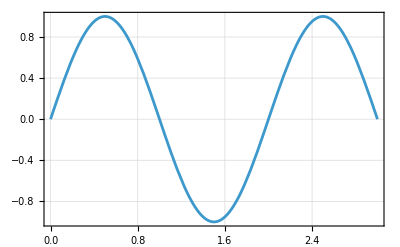

```mathematica
Plot[Sin[π x],{x,0,3},opts]/.opts->Sequence[Frame->True,GridLines->Automatic]
```

```mathematica
Unevaluated[Plot[Sin[π x],{x,0,3},opts]]/.opts->Sequence[Frame->True,GridLines->Automatic]
```

-Graphics-

### Exercise2 Use replacement by Nothing to remove the points from the Graphics expression that is created by this input:

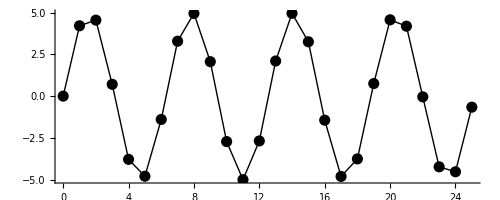

```mathematica
With[{pts=Table[{k,5Sin[k]},{k,0,25}]},Graphics[{Line[pts],PointSize[0.02],Point/@pts},Axes->True]]
```

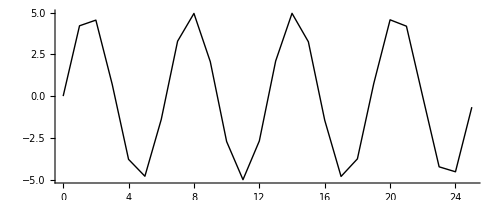

```mathematica
With[{pts=Table[{k,5Sin[k]},{k,0,25}]},Graphics[{Line[pts],PointSize[0.02],Point/@pts},Axes->True]]/. _Point -> Nothing
```

### Exercise3 Fix this program to step through the list using a Do loop, but to delete the ones as intended instead of failing after generating messages:

```mathematica
x={0,1,2,0,1,2,0,1,2};
Do[If[x[[k]]==1,x[[k]]=Nothing],{k,Length[x]}]
x
```

Part::partw: Part 7 of {0,2,1,0,1,2} does not exist.

Part::partw: Part 8 of {0,2,1,0,1,2} does not exist.

Part::partw: Part 9 of {0,2,1,0,1,2} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{0,2,1,0,1,2}

```mathematica
x={0,1,2,0,1,2,0,1,2};
Do[
If[x[[k]]==1,x[[k]]=Nothing],{k,Length[x],1,-1}]
x
```

{0,2,0,2,0,2}

```mathematica
ClearAll[x]
```

## Exercises: Dynamic Computation

### Exercise1 Make a Manipulate that displays Graphics[{c,Disk[]}] and with a RadioButtonBar control for setting the value of c to Blue, Green or Blue.

```mathematica
Manipulate[Graphics[{c,Disk[]}],{c,{Blue,Green,Red}},ControlType-> RadioButtonBar]
```

### Exercise2 Use DynamicModule to modify this program to localize the dynamic variable:

```mathematica
Panel[Column[{Slider[Dynamic[n],{0,10,1},Appearance->"Labeled"],Dynamic[Range[n]]}]]
```

|

```mathematica
DynamicModule[{n},Panel[Column[{Slider[Dynamic[n],{0,10,1},Appearance->"Labeled"],Dynamic[Range[n]]}]]]
```

### Exercise3 Modify this program so that the checkbox controls are displayed in a 2×2 grid on the left side of the display rather than in a column above the display:

```mathematica
Manipulate[Grid[{{x11,x12},{x21,x22}},Dividers->All],{x11,{Black,White}},{x12,{Black,White}},{x21,{Black,White}},{x22,{Black,White}},ControlType->Checkbox]
```

```mathematica
Manipulate[Grid[{{x11,x12},{x21,x22}},Dividers->All],{x11,{Black,White}},{x12,{Black,White}},{x21,{Black,White}},{x22,{Black,White}},ControlType->Checkbox,ControlPlacement->Left]
```

## Exercises: Constructing User Interface

### Exercise1 Change this Manipulate program to use a Locator control rather than a pair of sliders for controlling the location of a circle in a graphic:

```mathematica
Manipulate[Graphics[Circle[{x,y}],Axes->True,PlotRange->10],{{x,0},-10,10},{{y,0},-10,10}]
```

```mathematica
Manipulate[Graphics[Circle[pt],Axes->True,PlotRange->10],{{pt,{0,0}},Locator}]
```

### Exercise2 Use TabView to set up a display with tabs to choose among displaying a graphic containing a disk, a circle or a triangle ( Graphics[Disk[]] , Graphics[Circle[]], Graphics[Triangle[]]).

```mathematica
TabView[{disk->Graphics[Disk[]],circle->Graphics[Circle[]],triangle->Graphics[Triangle[]]}]
```

123

### Exercise3 Modify this FormPage input to use the “String” interpreter and to apply StringLength to the string that is entered:

```mathematica
FormPage[{{"x","enter an integer:"}->"ComputedInteger"},FactorInteger[#x]&]
```

```mathematica
FormPage[{{"x","enter a string:"}->"String"},StringLength[#x]&]
```

### Exercise4 Modify this program so that, instead of inserting “MAX” in place of elements larger than 10, the program puts up a blocking dialog box with a button to insert “MAX” and a button to insert Nothing in place of those elements. (Inserting Nothing will have the effect of deleting those elements from the list):

```mathematica
Map[
If[#>10,"MAX",#]&,
Range[12]
]
```

```mathematica
Map[If[#>10,DialogInput[Row[{DefaultButton["delete element",DialogReturn[Nothing]],CancelButton["insert MAX",DialogReturn["MAX"]]}]],#]&,Range[12]]
```

{1,2,3,4,5,6,7,8,9,10,MAX,MAX}

## Exercises: Knowledge Representation

### Exercise1 Use Hold and InputForm to get ArgentinapopulationYear:2010 in InputForm format(formattedusingexplicitEntityandEntityPropertyexpressions).

```mathematica
Entity["Country","Argentina"][]//Hold //InputForm
```

Hold[Entity["Country", "Argentina"][EntityProperty["Country", "Population", {"Date" -> DateObject[{2010}]}]]]

### Exercise2 Use EntityValue to get a list consisting of the name and mass of the planet Jupiter.

```mathematica
EntityValue[Entity["Planet", "Jupiter"], {"Name","Mass"}]
```

{Jupiter,1.898×10^27 kg}

### Exercise3 Find the list of entities represented by halogens.

```mathematica
EntityClass["Element","Halogen"]["Properties"]
```

{adiabatic index,allotropes,allotropic multiplicities,alternate names,atomic mass,atomic number,atomic radius,atomic symbol,block,Bohr model plot,boiling point T_b,Brinell hardness,bulk modulus,CAS number,color,common compound names,covalent radius,critical pressure p_c,critical temperature T_c,crust abundance,crust molar abundance,Bravais lattice,lattice schematic,Curie point,Debye characteristic temperature,decay mode,discoverers,discovery country,discovery date,electrical conductivity,electrical type,electron affinity,electron count,electronegativity,electronic configuration,electron shell configuration,entity classes,entity type list,molar heat of fusion Δ_fusH,gas atomic multiplicities,group,half-life,human abundance,human molar abundance,icon color,image,ionization energies,isotope abundances,isotope half-lives,isotope lifetimes,known isotopes,known oxidation states,lattice angles,lattice constants,Lewis dot structure,liquid density,magnetic type,mass density,mass magnetic susceptibility,melting point T_m,memberships,meteorite abundance,meteorite molar abundance,Mohs hardness,molar heat capacity,molar magnetic susceptibility,molar mass,molar radioactivity,molar volume,most common oxidation states,name,Néel point,number of neutrons per isotope,neutron cross-section,neutron mass absorption,nuclear diameter,nuclear radius,ocean abundance,ocean molar abundance,orbital occupation list,origins,period,phase at STP,Poisson ratio,price,proton count,refractive index,resistivity,series,shear modulus,short electronic configuration,solar abundance,solar molar abundance,molar heat of solidification,sound speed,space group,IUCr space group number,specific heat of fusion Δ_fush,specific heat capacity c_p,specific ionization energies,specific radioactivity,specific heat of solidification,stable isotopes,superconducting point,tensile yield strength,term symbol,thermal conductivity,thermal expansion,threshold frequency,ultimate tensile strength,universe abundance,universe molar abundance,unstable isotopes,valence,valence electron count,van der Waals radius,molar heat of vaporization Δ_vapH,Vickers hardness,volume magnetic susceptibility,work function,Young modulus}

```mathematica
Manipulate[x,{x,{1,2,3},ControlType->RadioButtonBar}]
```

```mathematica
Manipulate[{x,y},Row[{Control[{x,{0,1}}],Control[{y,{0,1}}]}]]
```

```mathematica
MenuView[{1->"one",2->"two",3->"three"}]
```

```mathematica
CreatePalette[{x,0,10}]
```

```mathematica
LocalTime[Entity["Country","CostaRica"]]
```

Tue 21 Apr 2026 04:59:26GMT-6

```mathematica
EntityList[EntityClass["Cloud","CloudTypes"]]
```

{altocumulus,altostratus,asperitas,cirrocumulus,cirrus,cirrostratus,cumulonimbus,cumulus,lenticular,nimbostratus,stratocumulus,stratus}

## Exercises: Making Plots of Data

### Exercise1 Modify this input so that the vertical scale is logarithmic and so the data is shown with plot markers with style Style[“■”,Large,Blue] joined by straight lines. Lines joining plot markers can be specified using the option Joined→True:

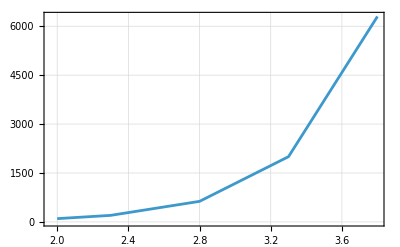

```mathematica
ListLinePlot[{{2,100},{2.3,200},{2.8,630},{3.3,2000},{3.8,6300}},Frame->True,GridLines->Automatic]
```

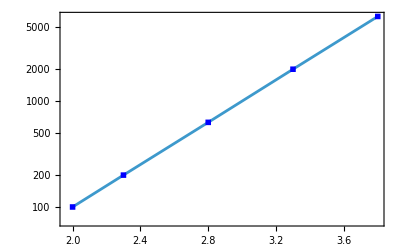

```mathematica
ListLinePlot[{{2,100},{2.3,200},{2.8,630},{3.3,2000},{3.8,6300}},Frame->True,GridLines->Automatic, ScalingFunctions->"Log", PlotMarkers -> Style["■",Large,Blue], Joined->True]
```

### Exercise2 Modify this input to show a callout label above each bar rather than a label below each bar:

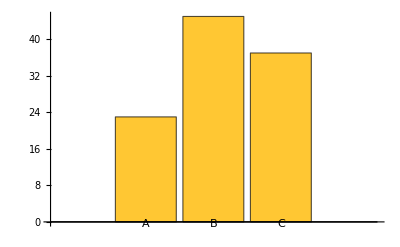

```mathematica
BarChart[{23,45,37},ChartLabels->{"A","B","C"}]
```

```mathematica
BarChart[{23,45,37},ChartLabels->Callout[{"A","B","C"}]]
```

-Graphics-

### Exercise3 This input uses Disk graphics primitives to construct a type of bubble chart. Use BubbleChart to make a bubble chart for the same data:

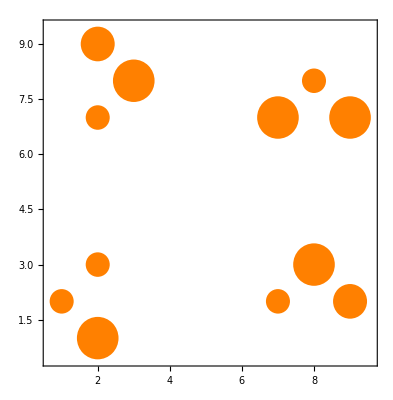

```mathematica
Graphics[{Orange,Apply[Disk[{#1,#2},Sqrt[#3]/3]&,{{1,2,1},{2,1,3},{2,3,1},{2,7,1},{3,8,3},{2,9,2},{7,2,1},{8,3,3},{9,2,2},{7,7,3},{9,7,3},{8,8,1}},{1}]},Frame->True]
```

```mathematica
BubbleChart[{{1,2,1},{2,1,3},{2,3,1},{2,7,1},{3,8,3},{2,9,2},{7,2,1},{8,3,3},{9,2,2},{7,7,3},{9,7,3},{8,8,1}}]
```

-Graphics-

## Exercises: Function Visualization

### Exercise1 Make a plot of the functions Exp[x], Exp[2x] and x^5, all on the same plot, for 1<x<10, and with a logarithmic vertical scale. Include the options GridLines→Automatic and Frame→True so that the plot is drawn with grid lines and a frame.

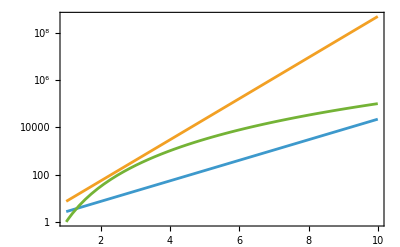

```mathematica
Plot[{Exp[x], Exp[2x], x^5},{x,1,10},ScalingFunctions->"Log", GridLines->Automatic,Frame->True]
```

### Exercise2 Change this input so that the vertical range goes from -6 to +6 and uses light gray shading rather than light red shading between the line and the axis:

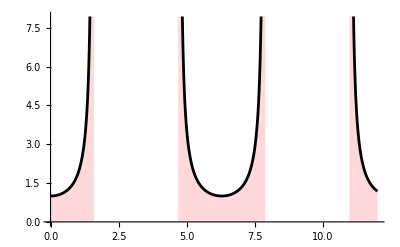

```mathematica
Plot[1/Cos[x],{x,0,12},PlotStyle->Black,Filling->{1->{Axis,LightRed}},PlotRange->{0,Automatic}]
```

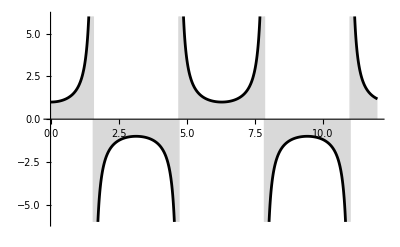

```mathematica
Plot[1/Cos[x],{x,0,12},PlotStyle->Black,Filling->{1->{Axis,LightGray}},PlotRange->{-6,6}]
```

#### Exercise3 Make a Manipulate to control a parametric plot of {xCos[t],(1-x)Sin[t]} for 0<t<2π, with a slider to control for x in the range -5<x<6, and with both the vertical and horizontal ranges in the plot fixed at -6 to 6.

```mathematica
Manipulate[ParametricPlot[{x Cos[t],(1-x)Sin[t]},{t,0,2Pi}, PlotRange->6],{x,-5,6}]
```

```mathematica
Manipulate[ParametricPlot[{x Cos[t],(1-x) Sin[t]},{t,1,5},PlotRange->6],{x,-5,6}]
```

## Exercises: Labeling Plots

### Exercise1 Add a frame and frame labels x and y for the horizontal and vertical scales in this plot, with all of the labels (including tick labels) given in 16 point font:

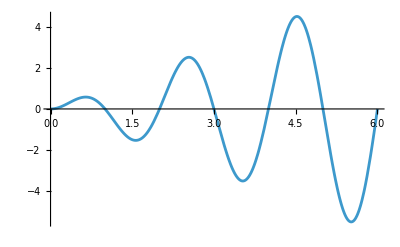

```mathematica
Plot[x Sin[π x],{x,0,6}]
```

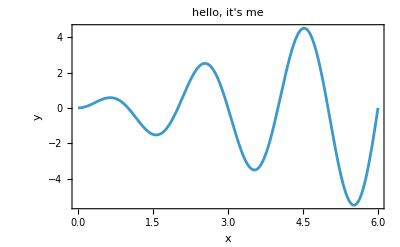

```mathematica
Plot[x Sin[π x],{x,0,6}, Frame->True, LabelStyle->16,FrameLabel->{"x", "y"}, PlotLabel->"hello, it's me" ]
```

### Exercise2 Add callout labels to the lines in this plot to label each line with the mathematical expression for the corresponding function. That is, the plot of Sqrt[x]Cos[x] should be labeled with xcos(x) and the plot of Sin[x] should be labeled with sin(x):

```mathematica
Plot[{Callout[Sqrt[x] Cos[x]],Callout[Sin[x]]},{x,0,5}]
```

-Graphics-

### Exercise3 Change this bar chart so that the bars start on the left side of the chart and extend to the right, and add a frame and labels in 12 point font with label A for the first bar, B for the second bar, C for the third bar, D for the fourth bar and E for the fifth bar:

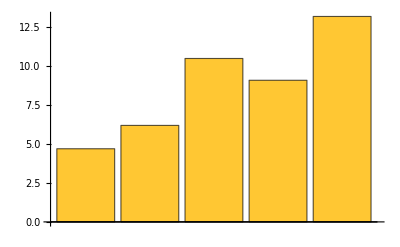

```mathematica
BarChart[{4.7,6.2,10.5,9.1,13.2}]
```

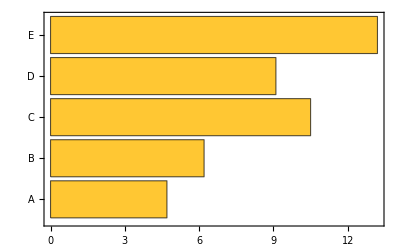

```mathematica
BarChart[{4.7,6.2,10.5,9.1,13.2}, BarOrigin->Left, Frame->True,LabelStyle->16, ChartLabels->{"A","B","C","D", "E"}]
```

```mathematica
data1 = {1,2,3,4,5,6};
data2={2,4,6,8,10};
```

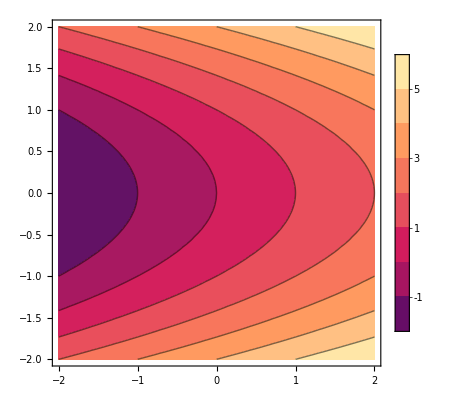

```mathematica
ContourPlot[x+y^2,{x,-2,2},{y,-2,2},PlotLegends->Automatic]
```

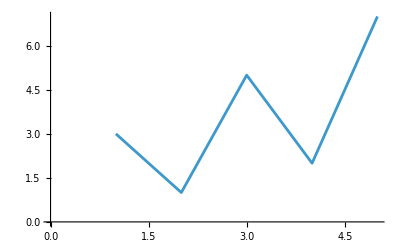

```mathematica
ListLinePlot[Tooltip[{3,1,5,2,7}]]
```

```mathematica
ListLinePlot[Tooltip/@{3,1,5,2,7}]
```

-Graphics-

```mathematica
ListLinePlot[{3,1,5,2,7},LabelStyle->Tooltip]
```

-Graphics-

```mathematica
ListLinePlot[{3,1,5,2,7},PlotLabels->Tooltip]
```

-Graphics-

```mathematica
BarChart[{1,Callout[2,"A"],3}]
```

-Graphics-

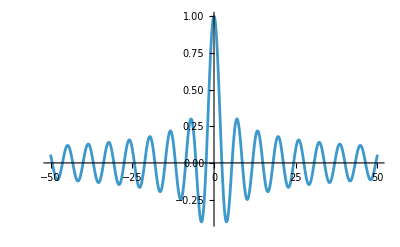

```mathematica
Plot[BesselJ[0,x],{x,-50,50},PlotRange->All]
```

## Exercises: Speed and Memory Performance

### Exercise1 After entering the following definitions for f, use Timing and ListLogPlot to make a plot with a logarithmic vertical scale of the time needed to evaluate f[n] for n from 1 to 30:

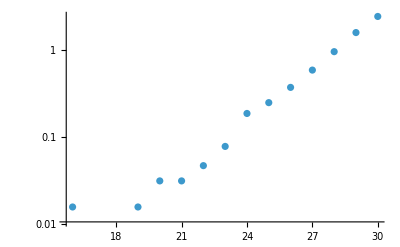

```mathematica
f[0]=1;
f[1]=1;
f[n_]:=f[n-1]+f[n-2]

ListLogPlot[Table[{n,First[Timing[f[n]]]},{n,30}]]
```

```mathematica
ClearAll[f]
```

### Exercise2 Modify this program to use Sow and Reap to accumulate the final result rather than Append:

```mathematica
n=0;
counter=0;
Reap[
While[counter<10,n=n+1;
If[PrimeQ[n],Sow[n];counter++]]][[2,1]]
```

{2,3,5,7,11,13,17,19,23,29}

## Exercises: Monitoring and Debugging

### Exercise1 Use Reap and Sow to modify this program so that the result of the evaluation includes the list of x’s that come up during the calculation:

```mathematica
Nest[Function[x,x+1],0,10]
```

10

```mathematica
Reap[Nest[Function[x,Sow[x]+1],0,10]]
```

{10,{{0,1,2,3,4,5,6,7,8,9}}}

### Exercise2 Modify this program using Monitor and ProgressIndicator so that a progress indicator bar showing the current value of k is displayed while the program is running:

```mathematica
result=0;For[k=0,k<=10,k++,result=result+k;Pause[0.2]];result
```

```mathematica
Monitor[result=0;For[k=0,k<=10,k++,result=result+k;Pause[0.2]];result ,ProgressIndicator[k,{0,10}]]
```

55

```mathematica
Compile[{{x,_Real,1}},Length[x]]
```

CompiledFunction[…]

```mathematica
Timing[3+4]
```

{0.,7}

```mathematica
Monitor[Table[Pause[1];k,{k,5}],k]
```

{1,2,3,4,5}

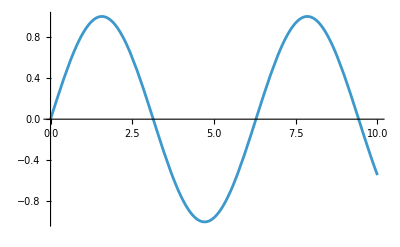
{-Graphics-,{{2.04082×10^-7,0.196287,0.409084,0.607779,0.802576,1.01388,1.21109,1.42481,1.63463,1.83035,2.04257,2.2407,2.43493,2.64567,2.84231,3.05546,3.26471,3.45986,3.67151,3.86907,4.08314,4.29331,4.48938,4.70196,4.90044,5.09502,5.30611,5.5031,5.7166,5.9262,6.1217,6.33371,6.53162,6.72563,6.93616,7.13258,7.34551,7.54434,7.73927,7.95071,8.14805,8.3619,8.57186,8.76771,8.98007,9.17833,9.3727,9.58357,9.78034,10.,0.0981434,0.705178,0.908231,1.11249,1.31795,1.52972,1.73249,1.93646,2.14164,2.33781,3.77029,3.97611,4.18823,4.39135,4.59567,4.8012,4.99773,5.20057,5.40461,5.60985,7.03437,7.23904,7.44492,7.6418,7.84499,8.04938,8.25498,8.46688,8.66978,9.89017,0.0490718,0.656478,0.855404,1.06319,1.26452,1.47726,1.68356,1.8834,2.09211,2.28926,3.7209,3.92259,4.13568,4.34233,4.54253,4.75158,4.94908,5.14779,5.35536,5.55647,6.98526,7.18581,7.39522,7.59307,7.79213,8.00005,8.20152,8.41439,8.62082,9.83526,0.961058,1.16179,1.37138,1.58217,1.78142,1.98952,4.02962,4.24077,4.44036,4.64882,4.85082,5.04637,5.25334,7.08347,7.29228,7.49463,7.69054,7.89785,8.09872,8.30844,9.94509,0.024536,0.632129,0.82899,1.03854,1.23781,1.45104,1.65909,1.85687,2.06734,2.26498,3.69621,3.89583,4.10941,4.31782,4.51595,4.72677,4.92476,5.12141,5.33073,5.52979,6.96071,7.15919,7.37036,7.5687,7.7657,7.97538,8.17478,8.38815,8.59634,9.8078,0.934644,1.13714,1.34466,1.55595,1.75695,1.96299,4.00287,4.2145,4.41586,4.62224,4.82601,5.02205,5.22695,7.05892,7.26566,7.46978,7.66617,7.87142,8.07405,8.28171,9.91763,1.29124,1.50349,1.70802,1.90993,4.36684,4.5691,4.77639,4.97341,7.42007,7.61744,7.81856,8.02472,8.22825,1.39809,1.6084,1.80588,4.46487,4.67539,4.87563,7.7149,7.92428,8.12339,9.97254,0.0122681,0.619954,0.815783,1.02621,1.22445,1.43792,1.64686,1.84361,2.05496,2.25284,3.68386,3.88245,4.09628,4.30557,4.50267,4.71437,4.9126,5.10821,5.31842,5.51644,6.94843,7.14589,7.35794,7.55652,7.75249,7.96305,8.16142,8.37503,8.5841,9.79407,0.921437,1.12481,1.33131,1.54283,1.74472,1.94972,3.98949,4.20136,4.4036,4.60896,4.8136,5.00989,5.21376,7.04664,7.25235,7.45735,7.65399,7.85821,8.06172,8.26834,9.9039,1.27788,1.49038,1.69579,1.89667,4.35458,4.55581,4.76399,4.96125,7.40764,7.60525,7.80535,8.01238,8.21488,1.38474,1.59529,1.79365,4.45262,4.6621,4.86322,7.70272,7.91107,8.11105,9.95881,1.46415,1.67132,4.52924,4.73918,7.77892,7.98771,1.35802,1.56906,4.63553,4.83841,7.67835,7.88464,1.5166,1.72025,4.58238,4.7888,7.83178,1.41145,1.62151,4.68867,7.72709,7.9375,9.98627,0.00613415,0.613866,0.80918,1.02005,1.21777,1.43137,1.64074,1.83698,2.04877,2.24677,3.67769,3.87576,4.08971,4.29944,4.49602,4.70816,4.90652,5.10162,5.31227,5.50977,6.9423,7.13923,7.35172,7.55043,7.74588,7.95688,8.15474,8.36847,8.57798,9.78721,0.914834,1.11865,1.32463,1.53627,1.7386,1.94309,3.9828,4.19479,4.39747,4.60231,4.8074,5.00381,5.20716,7.04051,7.2457,7.45114,7.6479,7.8516,8.05555,8.26166,9.89704,1.2712,1.48382,1.68967,1.89003,4.34846,4.54917,4.75778,4.95516,7.40143,7.59916,7.79874,8.00621,8.2082,1.37806,1.58873,1.78753,4.44649,4.65546,4.85702,7.69663,7.90446,8.10489,9.95195,1.45759,1.66521,4.5226,4.73297,7.77231,7.98155,1.35134,1.5625,4.62889,4.83221,7.67226,7.87803,1.51005,1.71414,4.57574,4.78259,7.82517,1.40477,1.61496,4.68203,7.721,7.93089,9.97941,1.65298,4.72057,7.75909,1.54939,4.6156,7.86481,1.49693,4.77019,7.81195,1.60184,4.66875,7.91767,4.74538,7.78552,1.57562,4.64217,7.89124,1.52316,7.83838,1.62807,4.69532,9.99314,0.00306718,0.610823,0.805878,1.01697,1.21443,1.42809,1.63769,1.83366,2.04567,2.24374,3.6746,3.87242,4.08643,4.29638,4.4927,4.70506,4.90348,5.09832,5.30919,5.50644,6.93923,7.1359,7.34862,7.54738,7.74257,7.9538,8.1514,8.36519,8.57492,9.78378,0.911532,1.11557,1.32129,1.533,1.73554,1.93978,3.97945,4.19151,4.39441,4.59899,4.8043,5.00077,5.20386,7.03744,7.24237,7.44803,7.64485,7.8483,8.05247,8.25832,9.8936,1.26786,1.48054,1.68662,1.88672,4.34539,4.54585,4.75468,4.95212,7.39832,7.59612,7.79543,8.00313,8.20486,1.37472,1.58545,1.78447,4.44343,4.65214,4.85392,7.69358,7.90116,8.1018,9.94852,1.45431,1.66215,4.51928,4.72987,7.769,7.97846,1.348,1.55922,4.62557,4.82911,7.66922,7.87473,1.50677,1.71108,4.57242,4.77949,7.82187,1.40143,1.61168,4.67871,7.71795,7.92759,9.97597,1.64992,4.71747,7.75579,1.54611,4.61228,7.86151,1.49366,4.76709,7.80865,1.59856,4.66542,7.91437,4.74228,7.78222,1.57234,4.63885,7.88794,1.51988,7.83508,1.62479,4.692,9.9897,4.71126,1.53955,7.8549,7.80204,1.59201,4.65878,4.73607,1.56578,7.88133,1.51333,7.82847,1.61824,4.68535,4.72367,1.55267,7.86812,7.81526,1.60512,4.67207,4.74848,1.57889,7.89455,7.84169,4.69864,9.99657}}}

```mathematica
Reap[Plot[Sin[x],{x,0,10},EvaluationMonitor:>Sow[x]]]
```

```mathematica
Table[2Echo[x],{x,3}]
```

1

2

3

{2,4,6}

```mathematica
Monitor[Table[Pause[1];x+1,{x,6}],x]
```

{2,3,4,5,6,7}

## Exercises: Datasets

### Exercise1 Add a new entry for cherry wood with a density of 630 and hardness of 4430 to the dataset below:

```mathematica
woodData=Dataset[<|"birch"-><|"density"->670,"hardness"->5600|>,"cedar"-><|"density"->380,"hardness"->4000|>,"maple"-><|"density"->700,"hardness"->3100|>|>]
```

```mathematica
woodData=Dataset[<|"birch"-><|"density"->670,"hardness"->5600|>,"cedar"-><|"density"->380,"hardness"->4000|>,"maple"-><|"density"->700,"hardness"->3100|>,"Cherry wood" -><|"density" -> 630, "hardness" -> 4430 |>|>]
```

### Exercise2 Round the entries to the nearest hundred and add “approximate” before the column names:

```mathematica
woodData=Dataset[Round[<|"birch"-><|"Approx. density"->670,"Approx. hardness"->5600|>,"cedar"-><|"Approx. density"->380,"Approx. hardness"->4000|>,"maple"-><|"Approx. density"->700,"Approx. hardness"->3100|>,"cherry"-><|"Approx. density"->630,"Approx. hardness"->4430|>|>,100]]
```

### Exercise3 Select entries whose density is divisible by 7:

```mathematica
woodData=Dataset[<|"birch"-><|"density"->670,"hardness"->5600|>,"cedar"-><|"density"->380,"hardness"->4000|>,"maple"-><|"density"->700,"hardness"->3100|>,"cherry"-><|"density"->630,"hardness"->4430|>|>]
```

```mathematica
Select[woodData,Mod[#density, 7] == 0 &]
```

## Exercises: Controlling Evaluation

### Exercise1 Add a value of the PlotLabel option to this input so that Solve[4x==x^3,x] appears as a label on the plot:

```mathematica
Plot[{Callout[4x,"solution",Automatic,2],x^3},{x,0,3}]
```

-Graphics-

```mathematica
Plot[{Callout[4x,"solution",Automatic,2],x^3},{x,0,3}, PlotLabel->HoldForm[Solve[4x==x^3,x]]]
```

-Graphics-

### Exercise2 Use Function to change this input so that the result shows the evaluated values of x and y:

```mathematica
Block[{x=2,y=2},Defer[x+y]]
```

x+y

```mathematica
Block[{x=2,y=2},Function[{p,q},Defer[p+p]][x,y]]
```

2+2

### Exercise3 Use Function to change this input so that the result is a list containing the even integers in the unevaluated list:

```mathematica
Select[Unevaluated[{1,2,3,4,Abort[]}],EvenQ]
```

$Aborted

```mathematica
Select[Unevaluated[{1,2,3,4,Abort[]}],Function[x,EvenQ[Unevaluated[x]],HoldAll]]
```

{2,4}

### Exercise4 Define a rule for f[p_List,n_Integer] that returns Table[pn,{x,5}], where pn is the element at position n in the list p, and that will work even if x has a global value, and without evaluating any other elements in p. For example:

```mathematica
x=99;f[{x,x^2,Abort[]},2]
```

```mathematica
SetAttributes[f,HoldAll]
f[p_List,n_Integer]:=Extract[Unevaluated[p],n,Function[pn,Table[pn,{x,5}],HoldAll]]
x=99;f[{x,x^2,Abort[]},2]
ClearAll[f,x]
```

{1,4,9,16,25}

## Exercises: Nonstandard Evaluation

### Exercise1 Define a function f that takes one argument and that returns the head of that argument; for example:

```mathematica
SetAttributes[f,HoldAll]
f[p_]:=Head[Unevaluated[p]]
f[2+2]
f[Abort[]]
f[Timing[]]
```

Plus

Abort

Timing

### Exercise2 Define a rule for f[x_Symbol,p_] that assigns ToString[p] where p is evaluated, and that works even if x already has a global value; for example:

```mathematica
x=99;f[x,Table[k,{k,3}]];x
```

```mathematica
SetAttributes[f,HoldFirst]
f[x_Symbol,p_]:=(x=ToString[p])
x=99;f[x,Table[k,{k,3}]];x
ClearAll[f,x]
```

{1, 2, 3}